```mathematica
diffEq=D[ψ[x,t],t]==𝒟 D[ψ[x,t],{x,2}]
```

ψ^(0,1)[x,t]==𝒟 ψ^(2,0)[x,t]

```mathematica
bc0=ψ[0,t]==𝒦 t
```

ψ[0,t]==t 𝒦

```mathematica
bc1=ψ[1,t]==0
```

ψ[1,t]==0

```mathematica
ic=ψ[x,0]==0
```

ψ[x,0]==0

```mathematica
sol=DSolve[{diffEq,bc0,bc1,ic},ψ[x,t],{x,t}]
```

{{ψ[x,t]→-t (-1+x) 𝒦+-(2 (1-ⅇ^(-π^2 t 𝒟 K[1]^2)) 𝒦 Sin[π x K[1]])/(π^3 K[1]^3)K[1]1∞}}

```mathematica
f[x_,t_,𝒟_,𝒦_]:=𝒦 t(1-x)-∑_(k=1)^20 (2𝒦(1-ⅇ^(-π^2 t 𝒟 k^2))Sin[π x k])/(π^3 k^3)
```

```mathematica
d=0
```

0

```mathematica
k=0.1
```

0.1

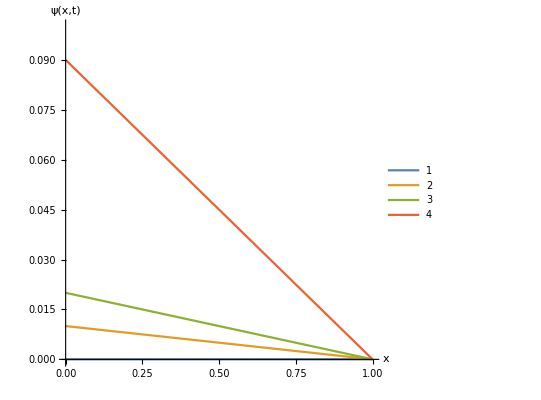

```mathematica
Plot[{f[x,0,d,k],f[x,0.1,d,k],f[x,0.2,d,k],f[x,0.9,d,k]},{x,0,1},PlotRange->{0,k},AxesLabel->{"x","ψ(x,t)"},PlotLegends->Automatic,AspectRatio->1]
```

This can’t be right. If 𝒟 is 0, then the profile should never change except at the x=0 boundary.